## Day 8: Two-Factor Authentication

### Input

```mathematica
input="rect 1x1
rotate row y=0 by 5
rect 1x1
rotate row y=0 by 5
rect 1x1
rotate row y=0 by 3
rect 1x1
rotate row y=0 by 2
rect 1x1
rotate row y=0 by 3
rect 1x1
rotate row y=0 by 2
rect 1x1
rotate row y=0 by 5
rect 1x1
rotate row y=0 by 5
rect 1x1
rotate row y=0 by 3
rect 1x1
rotate row y=0 by 2
rect 1x1
rotate row y=0 by 3
rect 2x1
rotate row y=0 by 2
rect 1x2
rotate row y=1 by 5
rotate row y=0 by 3
rect 1x2
rotate column x=30 by 1
rotate column x=25 by 1
rotate column x=10 by 1
rotate row y=1 by 5
rotate row y=0 by 2
rect 1x2
rotate row y=0 by 5
rotate column x=0 by 1
rect 4x1
rotate row y=2 by 18
rotate row y=0 by 5
rotate column x=0 by 1
rect 3x1
rotate row y=2 by 12
rotate row y=0 by 5
rotate column x=0 by 1
rect 4x1
rotate column x=20 by 1
rotate row y=2 by 5
rotate row y=0 by 5
rotate column x=0 by 1
rect 4x1
rotate row y=2 by 15
rotate row y=0 by 15
rotate column x=10 by 1
rotate column x=5 by 1
rotate column x=0 by 1
rect 14x1
rotate column x=37 by 1
rotate column x=23 by 1
rotate column x=7 by 2
rotate row y=3 by 20
rotate row y=0 by 5
rotate column x=0 by 1
rect 4x1
rotate row y=3 by 5
rotate row y=2 by 2
rotate row y=1 by 4
rotate row y=0 by 4
rect 1x4
rotate column x=35 by 3
rotate column x=18 by 3
rotate column x=13 by 3
rotate row y=3 by 5
rotate row y=2 by 3
rotate row y=1 by 1
rotate row y=0 by 1
rect 1x5
rotate row y=4 by 20
rotate row y=3 by 10
rotate row y=2 by 13
rotate row y=0 by 10
rotate column x=5 by 1
rotate column x=3 by 3
rotate column x=2 by 1
rotate column x=1 by 1
rotate column x=0 by 1
rect 9x1
rotate row y=4 by 10
rotate row y=3 by 10
rotate row y=1 by 10
rotate row y=0 by 10
rotate column x=7 by 2
rotate column x=5 by 1
rotate column x=2 by 1
rotate column x=1 by 1
rotate column x=0 by 1
rect 9x1
rotate row y=4 by 20
rotate row y=3 by 12
rotate row y=1 by 15
rotate row y=0 by 10
rotate column x=8 by 2
rotate column x=7 by 1
rotate column x=6 by 2
rotate column x=5 by 1
rotate column x=3 by 1
rotate column x=2 by 1
rotate column x=1 by 1
rotate column x=0 by 1
rect 9x1
rotate column x=46 by 2
rotate column x=43 by 2
rotate column x=24 by 2
rotate column x=14 by 3
rotate row y=5 by 15
rotate row y=4 by 10
rotate row y=3 by 3
rotate row y=2 by 37
rotate row y=1 by 10
rotate row y=0 by 5
rotate column x=0 by 3
rect 3x3
rotate row y=5 by 15
rotate row y=3 by 10
rotate row y=2 by 10
rotate row y=0 by 10
rotate column x=7 by 3
rotate column x=6 by 3
rotate column x=5 by 1
rotate column x=3 by 1
rotate column x=2 by 1
rotate column x=1 by 1
rotate column x=0 by 1
rect 9x1
rotate column x=19 by 1
rotate column x=10 by 3
rotate column x=5 by 4
rotate row y=5 by 5
rotate row y=4 by 5
rotate row y=3 by 40
rotate row y=2 by 35
rotate row y=1 by 15
rotate row y=0 by 30
rotate column x=48 by 4
rotate column x=47 by 3
rotate column x=46 by 3
rotate column x=45 by 1
rotate column x=43 by 1
rotate column x=42 by 5
rotate column x=41 by 5
rotate column x=40 by 1
rotate column x=33 by 2
rotate column x=32 by 3
rotate column x=31 by 2
rotate column x=28 by 1
rotate column x=27 by 5
rotate column x=26 by 5
rotate column x=25 by 1
rotate column x=23 by 5
rotate column x=22 by 5
rotate column x=21 by 5
rotate column x=18 by 5
rotate column x=17 by 5
rotate column x=16 by 5
rotate column x=13 by 5
rotate column x=12 by 5
rotate column x=11 by 5
rotate column x=3 by 1
rotate column x=2 by 5
rotate column x=1 by 5
rotate column x=0 by 1";
```

### Part 1

Display

```mathematica
W=50;
H=6;
init=ConstantArray[0,{H,W}];
```

```mathematica
SetAttributes[Rect,HoldFirst]
SetAttributes[RotateRow,HoldFirst]
SetAttributes[RotateCol,HoldFirst]
```

```mathematica
Rect[display_,x_,y_]:=display[[1;;y,1;;x]]=1;
RotateRow[display_,row_,n_]:=display[[row]]=RotateRight[display[[row]],n]
RotateCol[display_,col_,n_]:=display[[All,col]]=RotateRight[display[[All,col]],n]
```

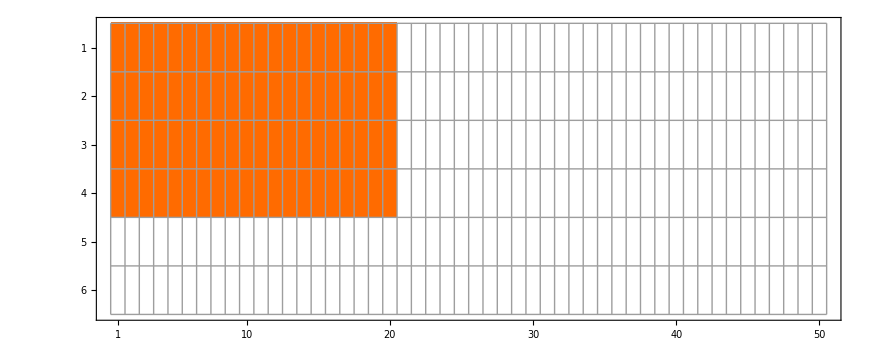

```mathematica
init=ConstantArray[0,{H,W}];
Rect[init,20,4];
MatrixPlot[init,Mesh->Automatic]
```

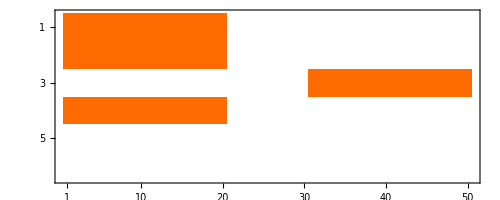

```mathematica
RotateRow[init,3,30];
init//MatrixPlot
```

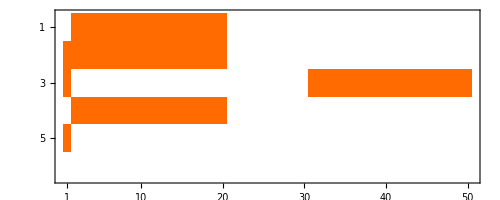

```mathematica
RotateCol[init,1,1];
init//MatrixPlot
```

```mathematica
commands=StringSplit[input,"\n"];
```

```mathematica
splittedCommands=StringSplit[#," "]&/@commands;
```

```mathematica
SetAttributes[ApplyCommand,HoldFirst];
ApplyCommand[display_,command_]:=Switch[command[[1]],
"rect",Rect[display,ToExpression@First@StringSplit[command⟦2⟧,"x"],ToExpression@Last@StringSplit[command⟦2⟧,"x"]],
"rotate",
Switch[command⟦2⟧,
"row",RotateRow[display,ToExpression@StringTake[command⟦3⟧,-1]+1,ToExpression@command⟦5⟧],
"column",RotateCol[display,(ToExpression@Last@StringSplit[command⟦3⟧,"="])+1,ToExpression@command⟦5⟧]]
]
```

```mathematica
init=ConstantArray[0,{H,W}];
init//MatrixPlot
```

-Graphics-

```mathematica
states={init};
counts={0};
```

```mathematica
Table[
ApplyCommand[init,splittedCommands[[i]]];
AppendTo[states,init];
AppendTo[counts,Total@Total@init]
If[states[[-1]]==states[[-2]],Print["No change: "<>ToString@i]],{i,1,Length@splittedCommands}];
```

```mathematica
states//Length
```

171

Number of cells lit

```mathematica
ToExpression[StringReplace[#,"x"->"*"]&/@(Select[splittedCommands,#[[1]]=="rect"&][[All,2]])]//Total
```

106

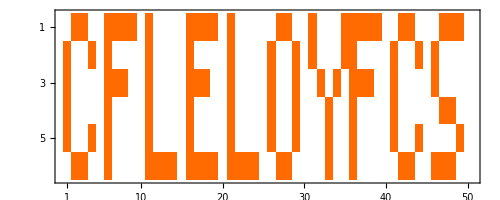

```mathematica
states//Last//MatrixPlot
```

```mathematica
Manipulate[
{MatrixPlot[states[[i]],ImageSize->800,Mesh->All,FrameTicks->Table[i,{i,50}]],If[i≤Length@splittedCommands,splittedCommands[[i]]],counts[[i]]},
{i,1,Length@states,1,Appearance->"Labeled"}]
```

```mathematica
states//Last//Total//Total
```

106

### Part 2

```mathematica
extstates=states~Join~Array[Last@states&,25];
```

```mathematica
frames=Table[MatrixPlot[extstates[[i]],ImageSize->800,Mesh->All,FrameTicks->Table[i,{i,50}]],{i,Length@extstates}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gyebro\Desktop\AoC2016

```mathematica
Export["AoC08.gif",frames]
```

AoC08.gif